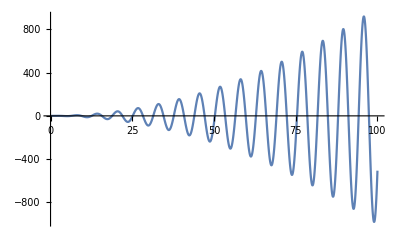

```mathematica
Plot[x^2*Sin[x]/10,{x,0,100}]
```

#### Classification

```mathematica
catagories = Table[Subscript[a, n] x^n,{n,0,10}]
```

{a_0,x a_1,x^2 a_2,x^3 a_3,x^4 a_4,x^5 a_5,x^6 a_6,x^7 a_7,x^8 a_8,x^9 a_9,x^10 a_10}

#### Regression

(we are given the whole signal as an input to the network), and as an output, we want it to tell us what type of polynomial it is. This is assuming our function is a polynomial

input signal →{sample taken at x_1
sample taken at x_2
sample taken at x_3
sample taken at x_4
sample taken at x_5→ {□
□
□
□
□
□
□
□
□

```mathematica
f[x_,a_,b_,c_,d_]:= a*Sin[b*x+c]+d
```

```mathematica
For[i=0,i<100,]
```

```mathematica
Clear[dataset]
dataset = {};
dataset = Append[dataset,Flatten[Table[{{x,f[x]}},{x,0,6,.1}],1]];
```

```mathematica
Prepend[dataset[[1]],{1,1,1,1}]
```

{{1,1,1,1},{0.,d+a Sin[0.+c]},{0.1,d+a Sin[0.1 b+c]},{0.2,d+a Sin[0.2 b+c]},{0.3,d+a Sin[0.3 b+c]},{0.4,d+a Sin[0.4 b+c]},{0.5,d+a Sin[0.5 b+c]},{0.6,d+a Sin[0.6 b+c]},{0.7,d+a Sin[0.7 b+c]},{0.8,d+a Sin[0.8 b+c]},{0.9,d+a Sin[0.9 b+c]},{1.,d+a Sin[1. b+c]},{1.1,d+a Sin[1.1 b+c]},{1.2,d+a Sin[1.2 b+c]},{1.3,d+a Sin[1.3 b+c]},{1.4,d+a Sin[1.4 b+c]},{1.5,d+a Sin[1.5 b+c]},{1.6,d+a Sin[1.6 b+c]},{1.7,d+a Sin[1.7 b+c]},{1.8,d+a Sin[1.8 b+c]},{1.9,d+a Sin[1.9 b+c]},{2.,d+a Sin[2. b+c]},{2.1,d+a Sin[2.1 b+c]},{2.2,d+a Sin[2.2 b+c]},{2.3,d+a Sin[2.3 b+c]},{2.4,d+a Sin[2.4 b+c]},{2.5,d+a Sin[2.5 b+c]},{2.6,d+a Sin[2.6 b+c]},{2.7,d+a Sin[2.7 b+c]},{2.8,d+a Sin[2.8 b+c]},{2.9,d+a Sin[2.9 b+c]},{3.,d+a Sin[3. b+c]},{3.1,d+a Sin[3.1 b+c]},{3.2,d+a Sin[3.2 b+c]},{3.3,d+a Sin[3.3 b+c]},{3.4,d+a Sin[3.4 b+c]},{3.5,d+a Sin[3.5 b+c]},{3.6,d+a Sin[3.6 b+c]},{3.7,d+a Sin[3.7 b+c]},{3.8,d+a Sin[3.8 b+c]},{3.9,d+a Sin[3.9 b+c]},{4.,d+a Sin[4. b+c]},{4.1,d+a Sin[4.1 b+c]},{4.2,d+a Sin[4.2 b+c]},{4.3,d+a Sin[4.3 b+c]},{4.4,d+a Sin[4.4 b+c]},{4.5,d+a Sin[4.5 b+c]},{4.6,d+a Sin[4.6 b+c]},{4.7,d+a Sin[4.7 b+c]},{4.8,d+a Sin[4.8 b+c]},{4.9,d+a Sin[4.9 b+c]},{5.,d+a Sin[5. b+c]},{5.1,d+a Sin[5.1 b+c]},{5.2,d+a Sin[5.2 b+c]},{5.3,d+a Sin[5.3 b+c]},{5.4,d+a Sin[5.4 b+c]},{5.5,d+a Sin[5.5 b+c]},{5.6,d+a Sin[5.6 b+c]},{5.7,d+a Sin[5.7 b+c]},{5.8,d+a Sin[5.8 b+c]},{5.9,d+a Sin[5.9 b+c]},{6.,d+a Sin[6. b+c]}}

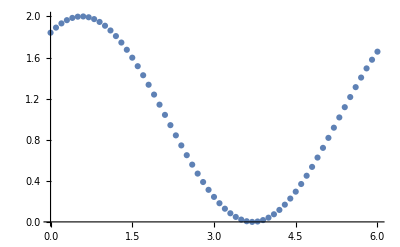

```mathematica
ListPlot[dataset]
```

```mathematica
Export["Source/python/neuralNetworks/testData/mydataset.txt",dataset,"CSV"]
```

Source/python/neuralNetworks/testData/mydataset.txt

```mathematica
SystemOpen["Source/python/neuralNetworks/testData/mydataset.txt"]
```